## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/8];
Length[%]
```

41

### Out-of-time-order correlations

```mathematica
OTOC[A_,B_,C_,D_,H_,β_,t_]:=Module[{ρβ=MatrixExp[-β/2 H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H],Ct=MatrixExp[-ⅈ t H].C.MatrixExp[ⅈ t H]},Tr[ρβ.At.B.ρβ.Ct.D]/Norm[ρβ,"Frobenius"]^2]
```

```mathematica
SiteCreateOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteAnnihilOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_otoc_sym/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
```

```mathematica
Subscript[otoc1, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc1.dat","Real64"],2]
Dimensions[%]
```

{0.564954+0. ⅈ,0.563924-0.0000457667 ⅈ,0.559174-0.00109231 ⅈ,0.547374-0.00629731 ⅈ,0.526038-0.0183808 ⅈ,0.493356-0.0348629 ⅈ,0.446619-0.0481503 ⅈ,0.383653-0.052132 ⅈ,0.307499-0.0484009 ⅈ,0.228614-0.0447647 ⅈ,0.160063-0.0473618 ⅈ,0.10916-0.0550601 ⅈ,0.0741482-0.0620104 ⅈ,0.0496063-0.0645885 ⅈ,0.0340675-0.0645963 ⅈ,0.0307848-0.0663788 ⅈ,0.0412631-0.0725167 ⅈ,0.059855-0.0827764 ⅈ,0.0763691-0.0961397 ⅈ,0.0845718-0.111904 ⅈ,0.0870236-0.127559 ⅈ,0.0898622-0.137556 ⅈ,0.0937067-0.137722 ⅈ,0.092138-0.130542 ⅈ,0.0784741-0.122705 ⅈ,0.0518037-0.116653 ⅈ,0.0172361-0.106282 ⅈ,-0.0172566-0.082322 ⅈ,-0.0442566-0.0426626 ⅈ,-0.0602276+0.00282226 ⅈ,-0.0679683+0.0388466 ⅈ,-0.075277+0.0570344 ⅈ,-0.0896506+0.0612023 ⅈ,-0.113327+0.0600415 ⅈ,-0.142479+0.0567017 ⅈ,-0.170216+0.0474926 ⅈ,-0.190324+0.0289981 ⅈ,-0.199451+0.00366726 ⅈ,-0.197497-0.0214636 ⅈ,-0.186677-0.0397571 ⅈ,-0.169916-0.0479992 ⅈ}

{41}

```mathematica
Subscript[otoc2, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc2.dat","Real64"],2]
Dimensions[%]
```

{0.566789+0. ⅈ,0.567681-0.000366067 ⅈ,0.574331-0.0000835638 ⅈ,0.591214+0.0119162 ⅈ,0.608795+0.0532442 ⅈ,0.599507+0.129346 ⅈ,0.535506+0.217496 ⅈ,0.41691+0.275428 ⅈ,0.280817+0.27436 ⅈ,0.175227+0.225552 ⅈ,0.12037+0.170518 ⅈ,0.096412+0.143064 ⅈ,0.0686018+0.141123 ⅈ,0.0235962+0.133995 ⅈ,-0.0169156+0.0961556 ⅈ,-0.0178119+0.0362575 ⅈ,0.0320053-0.00723241 ⅈ,0.104427-0.00145244 ⅈ,0.15546+0.0512309 ⅈ,0.159975+0.117431 ⅈ,0.126581+0.159105 ⅈ,0.0885453+0.159751 ⅈ,0.0775596+0.136489 ⅈ,0.0966369+0.126289 ⅈ,0.11628+0.155138 ⅈ,0.0948361+0.216482 ⅈ,0.00587403+0.268144 ⅈ,-0.132369+0.248767 ⅈ,-0.243484+0.127846 ⅈ,-0.243431-0.0379117 ⅈ,-0.13706-0.132103 ⅈ,-0.0331678-0.0993844 ⅈ,-0.0265332-0.00924785 ⅈ,-0.0964516+0.0350151 ⅈ,-0.157138+0.0142306 ⅈ,-0.168601-0.0172704 ⅈ,-0.15512-0.0191047 ⅈ,-0.14895+0.00289316 ⅈ,-0.157451+0.0249381 ⅈ,-0.169472+0.0324058 ⅈ,-0.172941+0.0280006 ⅈ}

{41}

```mathematica
Subscript[i, site]=1;
Subscript[j, site]=3;
```

```mathematica
(* reference calculation *)
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc1, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.564935,0.563901-0.0000441436 ⅈ,0.559139-0.00108907 ⅈ,0.547333-0.00629187 ⅈ,0.526001-0.0183708 ⅈ,0.493332-0.0348468 ⅈ,0.446612-0.0481289 ⅈ,0.383659-0.0521093 ⅈ,0.307507-0.0483804 ⅈ,0.228619-0.0447457 ⅈ,0.160069-0.0473406 ⅈ,0.109175-0.0550368 ⅈ,0.074174-0.0619914 ⅈ,0.0496369-0.0645812 ⅈ,0.034095-0.0646037 ⅈ,0.0308038-0.0663983 ⅈ,0.0412726-0.0725434 ⅈ,0.0598576-0.0828057 ⅈ,0.0763687-0.0961694 ⅈ,0.0845712-0.111932 ⅈ,0.0870224-0.12758 ⅈ,0.0898583-0.137568 ⅈ,0.0937-0.137722 ⅈ,0.0921311-0.130533 ⅈ,0.0784704-0.122693 ⅈ,0.0518029-0.116644 ⅈ,0.0172337-0.10628 ⅈ,-0.0172638-0.0823273 ⅈ,-0.0442678-0.0426724 ⅈ,-0.0602398+0.00281053 ⅈ,-0.0679789+0.0388344 ⅈ,-0.0752855+0.057023 ⅈ,-0.0896582+0.0611936 ⅈ,-0.113335+0.0600371 ⅈ,-0.142487+0.0567032 ⅈ,-0.170223+0.0475004 ⅈ,-0.190329+0.0290107 ⅈ,-0.199456+0.00368211 ⅈ,-0.197504-0.0214484 ⅈ,-0.186685-0.0397431 ⅈ,-0.169924-0.047988 ⅈ}

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc2, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.566776,0.567668-0.000366802 ⅈ,0.574316-0.0000870541 ⅈ,0.591193+0.0119058 ⅈ,0.608768+0.0532236 ⅈ,0.599478+0.129312 ⅈ,0.535484+0.21745 ⅈ,0.416903+0.27538 ⅈ,0.280824+0.274321 ⅈ,0.175241+0.225527 ⅈ,0.120385+0.170507 ⅈ,0.0964251+0.143059 ⅈ,0.0686152+0.14112 ⅈ,0.0236116+0.133994 ⅈ,-0.0169007+0.0961601 ⅈ,-0.0178025+0.0362688 ⅈ,0.0320064-0.00721817 ⅈ,0.104423-0.00144021 ⅈ,0.155456+0.0512397 ⅈ,0.159976+0.117437 ⅈ,0.126589+0.159109 ⅈ,0.088565+0.159755 ⅈ,0.077588+0.1365 ⅈ,0.0966642+0.12631 ⅈ,0.116298+0.155164 ⅈ,0.094845+0.216506 ⅈ,0.0058777+0.268162 ⅈ,-0.132366+0.24878 ⅈ,-0.243479+0.12786 ⅈ,-0.243429-0.0378926 ⅈ,-0.137063-0.132083 ⅈ,-0.0331743-0.0993696 ⅈ,-0.0265358-0.00924042 ⅈ,-0.0964496+0.0350182 ⅈ,-0.157137+0.0142312 ⅈ,-0.168605-0.0172724 ⅈ,-0.155129-0.0191095 ⅈ,-0.148963+0.00288373 ⅈ,-0.157467+0.024921 ⅈ,-0.169489+0.0323798 ⅈ,-0.172956+0.027969 ⅈ}

```mathematica
(* compare *)
Norm[Subscript[otoc1, list]-Subscript[otoc1, list,ref],∞]
```

0.0000412732

```mathematica
(* compare *)
Norm[Subscript[otoc2, list]-Subscript[otoc2, list,ref],∞]
```

0.0000506749

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

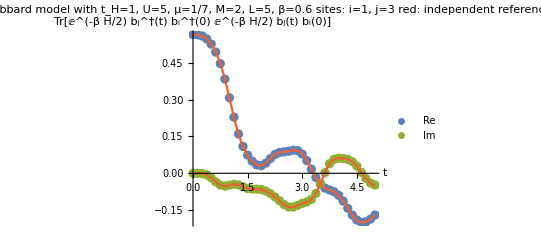

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc1, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc1, list]]}]},AxesLabel->{"t","Tr[ⅇ^(-β H/2) b_j^†(t) b_i^†(0) ⅇ^(-β H/2) b_j(t) b_i(0)]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc1, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc1, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc1_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

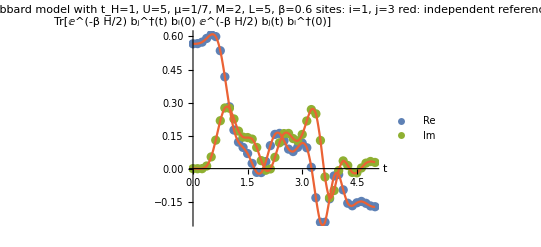

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc2, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc2, list]]}]},AxesLabel->{"t","Tr[ⅇ^(-β H/2) b_j^†(t) b_i(0) ⅇ^(-β H/2) b_j(t) b_i^†(0)]"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc2, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc2, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc2_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]={0,1/2,1,2,4,5};
```

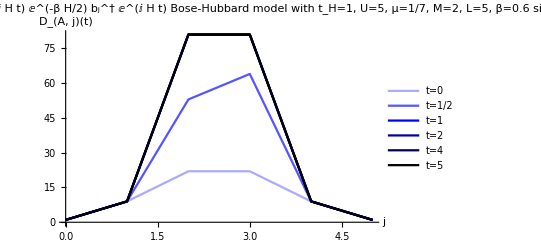

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import[Subscript[fn, import]<>"_DXA.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) ⅇ^(-β H/2) b_j^† ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

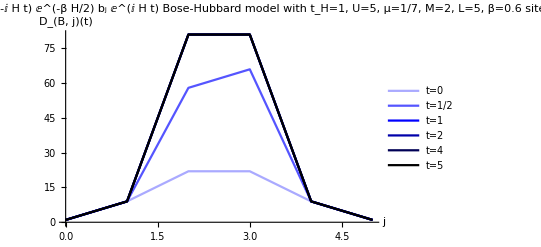

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import[Subscript[fn, import]<>"_DXB.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) ⅇ^(-β H/2) b_j ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H/2) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) ⅇ^(-β H/2) Subscript[b, j]^† ⅇ^(ⅈ H t) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{40,4}

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) ⅇ^(-β H/2) Subscript[b, j] ⅇ^(ⅈ H t) *)
Partition[Import[Subscript[fn, import]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10},{1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10}}

{40,4}